```mathematica
ClearAll[m, g, h, w, k, L, m, r, ϕ, θ]

eqn1 = -k*(r[t]-L)*Sin[ϕ[t]-θ[t]]*(h/2) == (1/12)*m*(w^2+h^2)*ϕ''[t];
eqn2 = -k*(r[t]-L)*Cos[ϕ[t]-θ[t]]+m*g*Cos[ϕ[t]] == m*((r''[t]-r[t]θ'[t]^2)*Cos[ϕ[t]-θ[t]]+(r[t]θ''[t]+2*r'[t]θ'[t])*Sin[ϕ[t]-θ[t]]-(h/2)*ϕ'[t]^2);
eqn3 = k*(r[t]-L)*Sin[ϕ[t]-θ[t]]-m*g*Sin[ϕ[t]] == m*(-(r''[t]-r[t]θ'[t]^2)*Sin[ϕ[t]-θ[t]]+(r[t]θ''[t]+2*r'[t]θ'[t])*Cos[ϕ[t]-θ[t]]+(h/2)*ϕ''[t]);

sol = Solve[{eqn1, eqn2, eqn3}, {ϕ''[t], r''[t], θ''[t]}];

{ode1, ode2, ode3} = {ϕ''[t], r''[t], θ''[t]} /. First@sol;

(*w = 15.24;
h = 22.86;
m = 0.584;
g = 9.81;
L = 0.263524;*)

kVal = (9.81*0.584)/0.04445;

vals = {w->0.1524, h->0.2286, m->0.584, g->9.81, k->kVal, L->0.263524};

ode1 = ϕ''[t] == ode1 /. vals;
ode2 = r''[t] == ode2 /. vals;
ode3 = θ''[t] == ode3 /. vals;

eqns = {ode1, ode2, ode3, θ[0]==0, ϕ[0]==Pi/4, r[0]==0.307975, θ'[0]==0, ϕ'[0]==0, r'[0]==0};
```

```mathematica
odeSol = NDSolve[eqns, {ϕ, θ, r}, {t, 0, 8}, Method->"StiffnessSwitching"]
```

{{ϕ→InterpolatingFunction[…],θ→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

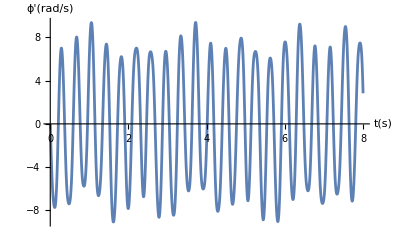

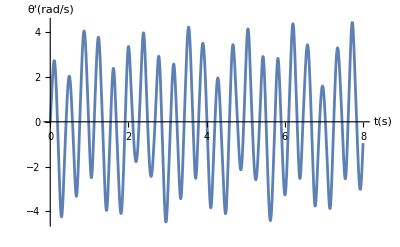

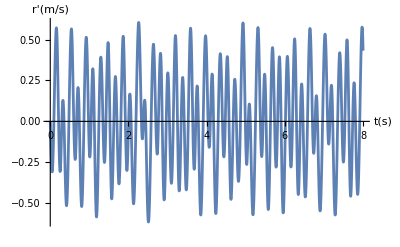

```mathematica
Plot[{ϕ'[t]}/. odeSol, {t, 0, 8},AxesLabel->{t [s], ϕ' [rad/s]}]
Plot[{θ'[t]}/. odeSol, {t, 0, 8}, AxesLabel->{t [s], θ' [rad/s]}]
Plot[r'[t]/. odeSol, {t,0,8}, AxesLabel->{t [s], r' [m/s]}]
```

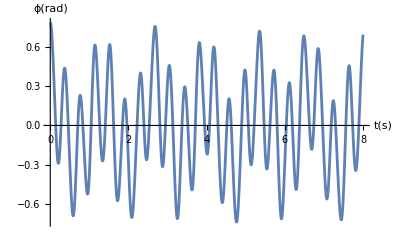

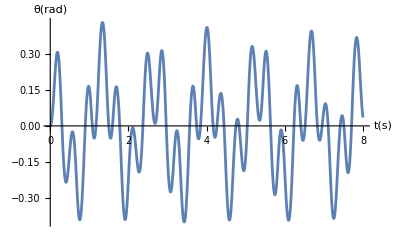

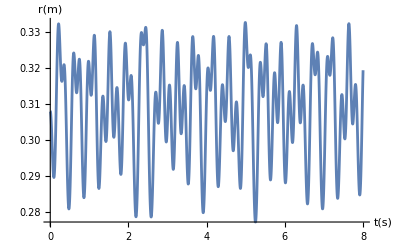

```mathematica
Plot[{ϕ[t]}/. odeSol, {t, 0, 8},AxesLabel->{t [s], ϕ [rad]}]
Plot[{θ[t]}/. odeSol, {t, 0, 8}, AxesLabel->{t [s], θ [rad]}]
Plot[r[t]/. odeSol, {t,0,8}, AxesLabel->{t [s], r [m]}]
```